```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[30]}->{V[30]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0,E0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[30]}->{V[30]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 28 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 18 Particles amplitudes

in total: 28 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

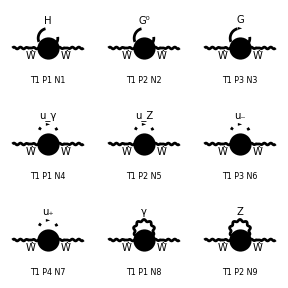

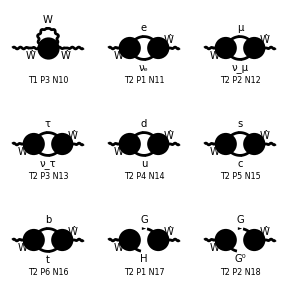

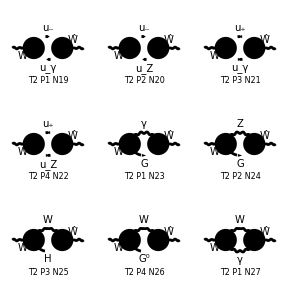

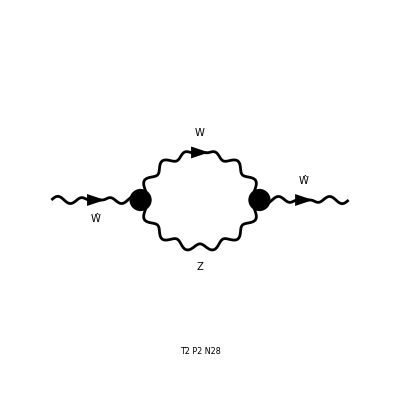

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/feynArts_amplitudes/OneLoopAmplitudes.m

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]:=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

```mathematica
t[Lor1_,Lor2_]:=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[30],p_,i_]->1,Conjugate[PolarizationVector][V[30],p_,i_]->1}
```

{ep[V[30],p_,i_]→1,ep^*[V[30],p_,i_]→1}

## Interference

```mathematica
myAmp1LnoEP=myAmp1L/.removePolarizationVectors;
```

```mathematica
AmpSquare[myAmp1LnoEP[[11]]l[Lor1,Lor2],1]
```

1/(24 π^4 psq)ⅈ EL^2 gWlN gWNl KiraPropagator[q1,0] KiraPropagator[-p1+q1,me] (psq SP[p1,q1]-2 SP[p1,q1]^2+psq SP[q1,q1])

```mathematica
myAmp1LLongitudinal=Map[#*l[Lor1,Lor2]&,myAmp1LnoEP];
```

```mathematica
SquareSimplifyAndSave[myAmp1LLongitudinal,{1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_18_1.m.

ABISS: Computed contribution 19-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_19_1.m.

ABISS: Computed contribution 20-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_20_1.m.

ABISS: Computed contribution 21-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_21_1.m.

ABISS: Computed contribution 22-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_22_1.m.

ABISS: Computed contribution 23-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_23_1.m.

ABISS: Computed contribution 24-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_24_1.m.

ABISS: Computed contribution 25-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_25_1.m.

ABISS: Computed contribution 26-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_26_1.m.

ABISS: Computed contribution 27-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_27_1.m.

ABISS: Computed contribution 28-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW//interferences/Contribution_28_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,28},{j,1}]
```

ABISS: Integral family {{B0, {mh}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_1_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_2_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_3_1.m.

ABISS: Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_4_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_5_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_6_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_7_1.m.

ABISS: Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_8_1.m.

ABISS: Integral family {{B0, {mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_9_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_10_1.m.

ABISS: Integral family {{E0, {me}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_11_1.m.

ABISS: Integral family {{E0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_12_1.m.

ABISS: Integral family {{E0, {ml}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_13_1.m.

ABISS: Integral family {{C0, {mu, md}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_14_1.m.

ABISS: Integral family {{C0, {mc, ms}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_15_1.m.

ABISS: Integral family {{C0, {mt, mb}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_16_1.m.

ABISS: Integral family {{C0, {mh, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_17_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_18_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_19_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_20_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_21_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_22_1.m.

ABISS: Integral family {{D0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_23_1.m.

ABISS: Integral family {{C0, {mw, mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_24_1.m.

ABISS: Integral family {{C0, {mh, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_25_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_26_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_27_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/interferences/Contribution_28_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,28},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_18_1.m.

ABISS: Computed contribution 19-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_19_1.m.

ABISS: Computed contribution 20-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_20_1.m.

ABISS: Computed contribution 21-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_21_1.m.

ABISS: Computed contribution 22-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_22_1.m.

ABISS: Computed contribution 23-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_23_1.m.

ABISS: Computed contribution 24-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_24_1.m.

ABISS: Computed contribution 25-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_25_1.m.

ABISS: Computed contribution 26-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_26_1.m.

ABISS: Computed contribution 27-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_27_1.m.

ABISS: Computed contribution 28-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WW/kira_input/Contribution_28_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{mh},1,0],userIntegral[B0,{mz},1,0],userIntegral[B0,{mw},1,0],userIntegral[A0,{0},1,0],userIntegral[E0,{me},0,1],userIntegral[E0,{me},1,0],userIntegral[E0,{me},1,1],userIntegral[E0,{me},-1,1],userIntegral[E0,{me},0,0],userIntegral[E0,{me},1,-1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{mm},-1,1],userIntegral[E0,{mm},0,0],userIntegral[E0,{mm},1,-1],userIntegral[E0,{ml},0,1],userIntegral[E0,{ml},1,0],userIntegral[E0,{ml},1,1],userIntegral[E0,{ml},-1,1],userIntegral[E0,{ml},0,0],userIntegral[E0,{ml},1,-1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},-1,1],userIntegral[C0,{mu,md},0,0],userIntegral[C0,{mu,md},1,-1],userIntegral[C0,{mc,ms},0,1],userIntegral[C0,{mc,ms},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},-1,1],userIntegral[C0,{mc,ms},0,0],userIntegral[C0,{mc,ms},1,-1],userIntegral[C0,{mt,mb},0,1],userIntegral[C0,{mt,mb},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},-1,1],userIntegral[C0,{mt,mb},0,0],userIntegral[C0,{mt,mb},1,-1],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mh,mw},1,0],userIntegral[C0,{mh,mw},-1,1],userIntegral[C0,{mh,mw},0,0],userIntegral[C0,{mh,mw},1,-1],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[C0,{mz,mw},-1,1],userIntegral[C0,{mz,mw},0,0],userIntegral[C0,{mz,mw},1,-1],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[E0,{mw},-1,1],userIntegral[E0,{mw},0,0],userIntegral[E0,{mw},1,-1],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{0},1,0]→0,userIntegral[E0,{m1},1,0]→0,userIntegral[E0,{m1},0,0]→0,userIntegral[E0,{m1},1,-1]→0,userIntegral[C0,{m1,m2},0,0]→0,userIntegral[E0,{m1},0,1]→userIntegral[B0,{m1},1,0],userIntegral[E0,{m1},1,1]→userIntegral[D0,{m1},1,1],userIntegral[E0,{m1},-1,1]→(m1^2+psq) userIntegral[B0,{m1},1,0],userIntegral[C0,{m1,m2},1,0]→userIntegral[B0,{m1},1,0],userIntegral[C0,{m1,m2},-1,1]→(-m1^2+m2^2+psq) userIntegral[C0,{m1,m2},0,1],userIntegral[C0,{m1,m2},1,-1]→(m1^2-m2^2+psq) userIntegral[B0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{mh},1,0],userIntegral[B0,{mz},1,0],userIntegral[B0,{mw},1,0],userIntegral[A0,{0},1,0],userIntegral[E0,{me},0,1],userIntegral[E0,{me},1,0],userIntegral[E0,{me},1,1],userIntegral[E0,{me},-1,1],userIntegral[E0,{me},0,0],userIntegral[E0,{me},1,-1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{mm},-1,1],userIntegral[E0,{mm},0,0],userIntegral[E0,{mm},1,-1],userIntegral[E0,{ml},0,1],userIntegral[E0,{ml},1,0],userIntegral[E0,{ml},1,1],userIntegral[E0,{ml},-1,1],userIntegral[E0,{ml},0,0],userIntegral[E0,{ml},1,-1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},-1,1],userIntegral[C0,{mu,md},0,0],userIntegral[C0,{mu,md},1,-1],userIntegral[C0,{mc,ms},0,1],userIntegral[C0,{mc,ms},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mc,ms},-1,1],userIntegral[C0,{mc,ms},0,0],userIntegral[C0,{mc,ms},1,-1],userIntegral[C0,{mt,mb},0,1],userIntegral[C0,{mt,mb},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mt,mb},-1,1],userIntegral[C0,{mt,mb},0,0],userIntegral[C0,{mt,mb},1,-1],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mh,mw},1,0],userIntegral[C0,{mh,mw},-1,1],userIntegral[C0,{mh,mw},0,0],userIntegral[C0,{mh,mw},1,-1],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[C0,{mz,mw},-1,1],userIntegral[C0,{mz,mw},0,0],userIntegral[C0,{mz,mw},1,-1],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[E0,{mw},-1,1],userIntegral[E0,{mw},0,0],userIntegral[E0,{mw},1,-1],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{mh},1,0],userIntegral[B0,{mz},1,0],userIntegral[B0,{mw},1,0],userIntegral[B0,{me},1,0],userIntegral[D0,{me},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ml},1,0],userIntegral[D0,{ml},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[B0,{mc},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[B0,{mt},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,28},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,28}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gHHWW)/(96 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL^2 gXXWW)/(96 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL^2 gFFWW)/(48 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ EL^2 ggzgzWW)/(24 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggmgmWW)/(48 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggpgpWW)/(48 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ d EL^2 gWWZZ)/(48 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ d EL^2 gWWWW)/(48 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,(ⅈ EL^2 gWlN gWNl)/(16 π^4)+(ⅈ EL^2 gWlN gWNl (me^2-psq))/(24 π^4 psq)-(ⅈ EL^2 gWlN gWNl (me^2+psq))/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl (me^2-psq))/(48 π^4)-(ⅈ EL^2 gWlN gWNl (me^2-psq)^2)/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(ⅈ EL^2 gWlN gWNl)/(16 π^4)+(ⅈ EL^2 gWlN gWNl (mm^2-psq))/(24 π^4 psq)-(ⅈ EL^2 gWlN gWNl (mm^2+psq))/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl (mm^2-psq))/(48 π^4)-(ⅈ EL^2 gWlN gWNl (mm^2-psq)^2)/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(ⅈ EL^2 gWlN gWNl)/(16 π^4)+(ⅈ EL^2 gWlN gWNl (ml^2-psq))/(24 π^4 psq)-(ⅈ EL^2 gWlN gWNl (ml^2+psq))/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl (ml^2-psq))/(48 π^4)-(ⅈ EL^2 gWlN gWNl (ml^2-psq)^2)/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud CKM[1,1] CKMC[1,1])/(16 π^4)-(ⅈ EL^2 gWdu gWud (md^2-mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(ⅈ EL^2 gWdu gWud (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(8 π^4 psq),-(ⅈ EL^2 gWdu gWud CKM[1,1] CKMC[1,1])/(16 π^4)+(ⅈ EL^2 gWdu gWud (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq),(ⅈ EL^2 gWdu gWud mu^2 CKM[1,1] CKMC[1,1])/(8 π^4)-(ⅈ EL^2 gWdu gWud (md^2-mu^2-psq) CKM[1,1] CKMC[1,1])/(16 π^4)-(ⅈ EL^2 gWdu gWud (-md^2+mu^2+psq)^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud CKM[2,2] CKMC[2,2])/(16 π^4)-(ⅈ EL^2 gWdu gWud (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(8 π^4 psq)-(ⅈ EL^2 gWdu gWud (-mc^2+ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud CKM[2,2] CKMC[2,2])/(16 π^4)+(ⅈ EL^2 gWdu gWud (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),(ⅈ EL^2 gWdu gWud mc^2 CKM[2,2] CKMC[2,2])/(8 π^4)+(ⅈ EL^2 gWdu gWud (mc^2-ms^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4)-(ⅈ EL^2 gWdu gWud (mc^2-ms^2+psq)^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gWdu gWud CKM[3,3] CKMC[3,3])/(16 π^4)-(ⅈ EL^2 gWdu gWud (mb^2-mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(ⅈ EL^2 gWdu gWud (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(8 π^4 psq),-(ⅈ EL^2 gWdu gWud CKM[3,3] CKMC[3,3])/(16 π^4)+(ⅈ EL^2 gWdu gWud (-mb^2+mt^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(ⅈ EL^2 gWdu gWud mt^2 CKM[3,3] CKMC[3,3])/(8 π^4)-(ⅈ EL^2 gWdu gWud (mb^2-mt^2-psq) CKM[3,3] CKMC[3,3])/(16 π^4)-(ⅈ EL^2 gWdu gWud (-mb^2+mt^2+psq)^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),0,0,0,0,0,0},{(ⅈ EL^2 gHFW^2)/(24 π^4)-(ⅈ EL^2 gHFW^2 (mh^2-mw^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gHFW^2 psq)/(48 π^4)-(ⅈ EL^2 gHFW^2 (mh^2-mw^2+psq))/(24 π^4)+(ⅈ EL^2 gHFW^2 (mh^2-mw^2+psq)^2)/(48 π^4 psq),-(ⅈ EL^2 gHFW^2)/(24 π^4)+(ⅈ EL^2 gHFW^2 (mh^2-mw^2+psq))/(24 π^4 psq)+(ⅈ EL^2 gHFW^2 (-mh^2+mw^2+psq))/(48 π^4 psq),0,0,0,0},{0,(ⅈ EL^2 gXFW^2)/(24 π^4)+(ⅈ EL^2 gXFW^2 (mw^2-mz^2-psq))/(24 π^4 psq)+(ⅈ EL^2 gXFW^2 (-mw^2+mz^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gXFW^2 (mw^2-mz^2-psq))/(24 π^4)+(ⅈ EL^2 gXFW^2 psq)/(48 π^4)+(ⅈ EL^2 gXFW^2 (-mw^2+mz^2+psq)^2)/(48 π^4 psq),-(ⅈ EL^2 gXFW^2)/(24 π^4)-(ⅈ EL^2 gXFW^2 (mw^2-mz^2-psq))/(24 π^4 psq)+(ⅈ EL^2 gXFW^2 (mw^2-mz^2+psq))/(48 π^4 psq),0,0},{0,0,(ⅈ EL^2 ggagmW^2)/(24 π^4)+(ⅈ EL^2 ggagmW^2 (mw^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggagmW^2 (mw^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggagmW^2 (mw^2-psq))/(24 π^4)-(ⅈ EL^2 ggagmW^2 (mw^2-psq)^2)/(48 π^4 psq)-(ⅈ EL^2 ggagmW^2 psq)/(48 π^4),0},{0,-(ⅈ EL^2 ggzgmW^2)/(24 π^4)-(ⅈ EL^2 ggzgmW^2 (mw^2-mz^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggzgmW^2 (-mw^2+mz^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggzgmW^2 (mw^2-mz^2-psq))/(24 π^4)-(ⅈ EL^2 ggzgmW^2 psq)/(48 π^4)-(ⅈ EL^2 ggzgmW^2 (-mw^2+mz^2+psq)^2)/(48 π^4 psq),(ⅈ EL^2 ggzgmW^2)/(24 π^4)+(ⅈ EL^2 ggzgmW^2 (mw^2-mz^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggzgmW^2 (mw^2-mz^2+psq))/(48 π^4 psq),0,0},{0,0,(ⅈ EL^2 ggagpW^2)/(24 π^4)+(ⅈ EL^2 ggagpW^2 (mw^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggagpW^2 (mw^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggagpW^2 (mw^2-psq))/(24 π^4)-(ⅈ EL^2 ggagpW^2 (mw^2-psq)^2)/(48 π^4 psq)-(ⅈ EL^2 ggagpW^2 psq)/(48 π^4),0},{0,-(ⅈ EL^2 ggzgpW^2)/(24 π^4)-(ⅈ EL^2 ggzgpW^2 (mw^2-mz^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggzgpW^2 (-mw^2+mz^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggzgpW^2 (mw^2-mz^2-psq))/(24 π^4)-(ⅈ EL^2 ggzgpW^2 psq)/(48 π^4)-(ⅈ EL^2 ggzgpW^2 (-mw^2+mz^2+psq)^2)/(48 π^4 psq),(ⅈ EL^2 ggzgpW^2)/(24 π^4)+(ⅈ EL^2 ggzgpW^2 (mw^2-mz^2-psq))/(24 π^4 psq)-(ⅈ EL^2 ggzgpW^2 (mw^2-mz^2+psq))/(48 π^4 psq),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(12 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ cw^2 EL^2 gFZW^2)/(24 π^4)-(ⅈ cw^4 EL^2 gFZW^2)/(48 π^4 sw^2)-(ⅈ EL^2 gFZW^2 sw^2)/(48 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gHWW^2)/(48 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gXWW^2)/(48 π^4),0,0,0},{0,0,-(ⅈ d EL^2 gWWA^2)/(24 π^4)-(ⅈ d EL^2 gWWA^2 (mw^2-psq))/(24 π^4 psq)+(ⅈ d EL^2 gWWA^2 (mw^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ d EL^2 gWWA^2 (mw^2-psq))/(24 π^4)+(ⅈ d EL^2 gWWA^2 (mw^2-psq)^2)/(48 π^4 psq)+(ⅈ d EL^2 gWWA^2 psq)/(48 π^4),0},{0,(ⅈ d EL^2 gWWZ^2)/(24 π^4)+(ⅈ d EL^2 gWWZ^2 (mw^2-mz^2-psq))/(24 π^4 psq)+(ⅈ d EL^2 gWWZ^2 (-mw^2+mz^2+psq))/(48 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ d EL^2 gWWZ^2 (mw^2-mz^2-psq))/(24 π^4)+(ⅈ d EL^2 gWWZ^2 psq)/(48 π^4)+(ⅈ d EL^2 gWWZ^2 (-mw^2+mz^2+psq)^2)/(48 π^4 psq),-(ⅈ d EL^2 gWWZ^2)/(24 π^4)-(ⅈ d EL^2 gWWZ^2 (mw^2-mz^2-psq))/(24 π^4 psq)+(ⅈ d EL^2 gWWZ^2 (mw^2-mz^2+psq))/(48 π^4 psq),0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients//Simplify
```

{-(ⅈ EL^2 (2 gHFW^2 (mh^2-mw^2-psq)+gHHWW psq))/(96 π^4 psq),1/(96 π^4 psq)ⅈ EL^2 (2 d gWWZ^2 mw^2+2 gXFW^2 mw^2-2 d gWWZ^2 mz^2-2 gXFW^2 mz^2+4 ggzgzWW psq+2 d gWWZ^2 psq+2 d gWWZZ psq+2 gXFW^2 psq-gXXWW psq-2 ggzgmW^2 (mw^2-mz^2+psq)-2 ggzgpW^2 (mw^2-mz^2+psq)),1/(48 π^4 psq)ⅈ EL^2 (-d gWWA^2 mw^2+ggagmW^2 (mw^2-psq)+ggagpW^2 (mw^2-psq)-gFFWW psq+ggmgmWW psq+ggpgpWW psq+d gWWA^2 psq-d gWWWW psq),(ⅈ EL^2 gWlN gWNl me^2)/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl me^2 (me^2-psq))/(48 π^4 psq),(ⅈ EL^2 gWlN gWNl mm^2)/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl mm^2 (mm^2-psq))/(48 π^4 psq),(ⅈ EL^2 gWlN gWNl ml^2)/(48 π^4 psq),-(ⅈ EL^2 gWlN gWNl ml^2 (ml^2-psq))/(48 π^4 psq),(ⅈ EL^2 gWdu gWud (md^2-mu^2) CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (md^2-mu^2) CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(16 π^4 psq),(ⅈ EL^2 gWdu gWud (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (mc^4+ms^4-ms^2 psq-mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(16 π^4 psq),(ⅈ EL^2 gWdu gWud (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(ⅈ EL^2 gWdu gWud (mb^4+mt^4-mt^2 psq-mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(ⅈ EL^2 (gHFW^2 (mh^2-mw^2)^2-gHWW^2 psq))/(48 π^4 psq),(ⅈ EL^2 gHFW^2 (mh^2-mw^2+psq))/(48 π^4 psq),-1/(48 π^4 psq)ⅈ EL^2 (-d gWWZ^2 mw^4-gXFW^2 mw^4+2 d gWWZ^2 mw^2 mz^2+2 gXFW^2 mw^2 mz^2-d gWWZ^2 mz^4-gXFW^2 mz^4+ggzgmW^2 (mw^2-mz^2)^2+ggzgpW^2 (mw^2-mz^2)^2+gXWW^2 psq),(ⅈ EL^2 (ggzgmW^2+ggzgpW^2-d gWWZ^2-gXFW^2) (mw^2-mz^2-psq))/(48 π^4 psq),-(ⅈ EL^2 (ggagmW^2 mw^4+ggagpW^2 mw^4-d gWWA^2 mw^4+4 gFAW^2 psq))/(48 π^4 psq),-(ⅈ EL^2 gFZW^2 (cw^2-sw^2)^2)/(48 π^4 sw^2)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters;
```

```mathematica
cfinal=coefficients/.parameterReplace//Simplify
```

{-(ⅈ EL^2 (mh^2-mw^2))/(192 π^4 psq sw^2),(ⅈ (1+4 cw^2 (-2+d)) EL^2 (mw^2-mz^2))/(192 π^4 psq sw^2),(ⅈ EL^2 (-2 (-2+d) mw^2 sw^2+psq (3-4 sw^2+2 d (-1+sw^2))))/(96 π^4 psq sw^2),(ⅈ EL^2 me^2)/(96 π^4 psq sw^2),-(ⅈ EL^2 me^2 (me^2-psq))/(96 π^4 psq sw^2),(ⅈ EL^2 mm^2)/(96 π^4 psq sw^2),-(ⅈ EL^2 mm^2 (mm^2-psq))/(96 π^4 psq sw^2),(ⅈ EL^2 ml^2)/(96 π^4 psq sw^2),-(ⅈ EL^2 ml^2 (ml^2-psq))/(96 π^4 psq sw^2),(ⅈ EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(ⅈ EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(ⅈ EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(ⅈ EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(ⅈ EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),-(ⅈ EL^2 (mc^4+ms^4-ms^2 psq-mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(ⅈ EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),-(ⅈ EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),-(ⅈ EL^2 (mb^4+mt^4-mt^2 psq-mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(ⅈ EL^2 (mh^4-2 mh^2 mw^2+mw^4-4 mw^2 psq))/(192 π^4 psq sw^2),(ⅈ EL^2 (mh^2-mw^2+psq))/(192 π^4 psq sw^2),(ⅈ EL^2 ((1+4 cw^2 (-2+d)) mw^4+(1+4 cw^2 (-2+d)) mz^4-2 mw^2 ((1+4 cw^2 (-2+d)) mz^2+2 psq)))/(192 π^4 psq sw^2),-(ⅈ (1+4 cw^2 (-2+d)) EL^2 (mw^2-mz^2-psq))/(192 π^4 psq sw^2),(ⅈ EL^2 ((-2+d) mw^4-4 mw^2 psq))/(48 π^4 psq),-(ⅈ EL^2 mw^2 (cw^2-sw^2)^2)/(48 cw^2 π^4 sw^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{mh},1,0],userIntegral[B0,{mz},1,0],userIntegral[B0,{mw},1,0],userIntegral[B0,{me},1,0],userIntegral[D0,{me},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ml},1,0],userIntegral[D0,{ml},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[B0,{mc},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[B0,{mt},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
c=-I cfinal/.{mw->mz cw} //Simplify
```

{-(EL^2 (mh^2-cw^2 mz^2))/(192 π^4 psq sw^2),((-1+cw^2) (1+4 cw^2 (-2+d)) EL^2 mz^2)/(192 π^4 psq sw^2),(EL^2 (-2 cw^2 (-2+d) mz^2 sw^2+psq (3-4 sw^2+2 d (-1+sw^2))))/(96 π^4 psq sw^2),(EL^2 me^2)/(96 π^4 psq sw^2),-(EL^2 me^2 (me^2-psq))/(96 π^4 psq sw^2),(EL^2 mm^2)/(96 π^4 psq sw^2),-(EL^2 mm^2 (mm^2-psq))/(96 π^4 psq sw^2),(EL^2 ml^2)/(96 π^4 psq sw^2),-(EL^2 ml^2 (ml^2-psq))/(96 π^4 psq sw^2),(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq sw^2),-(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),-(EL^2 (mc^4+ms^4-ms^2 psq-mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq sw^2),(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),-(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),-(EL^2 (mb^4+mt^4-mt^2 psq-mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq sw^2),(EL^2 (mh^4-2 cw^2 mh^2 mz^2+cw^4 mz^4-4 cw^2 mz^2 psq))/(192 π^4 psq sw^2),(EL^2 (mh^2-cw^2 mz^2+psq))/(192 π^4 psq sw^2),(EL^2 ((-1+cw^2)^2 (1+4 cw^2 (-2+d)) mz^4-4 cw^2 mz^2 psq))/(192 π^4 psq sw^2),-((1+4 cw^2 (-2+d)) EL^2 ((-1+cw^2) mz^2-psq))/(192 π^4 psq sw^2),(EL^2 (cw^4 (-2+d) mz^4-4 cw^2 mz^2 psq))/(48 π^4 psq),-(EL^2 mz^2 (cw^2-sw^2)^2)/(48 π^4 sw^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{mh},1,0],userIntegral[B0,{mz},1,0],userIntegral[B0,{mw},1,0],userIntegral[B0,{me},1,0],userIntegral[D0,{me},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ml},1,0],userIntegral[D0,{ml},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mc,ms},0,1],userIntegral[B0,{mc},1,0],userIntegral[C0,{mc,ms},1,1],userIntegral[C0,{mt,mb},0,1],userIntegral[B0,{mt},1,0],userIntegral[C0,{mt,mb},1,1],userIntegral[C0,{mh,mw},1,1],userIntegral[C0,{mh,mw},0,1],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
out=Plus@@(c m)
```

(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2] userIntegral[B0,{mc},1,0])/(32 π^4 psq SW^2)+(EL^2 me^2 userIntegral[B0,{me},1,0])/(96 π^4 psq SW^2)-(EL^2 (mh^2-cw^2 mz^2) userIntegral[B0,{mh},1,0])/(192 π^4 psq SW^2)+(EL^2 ml^2 userIntegral[B0,{ml},1,0])/(96 π^4 psq SW^2)+(EL^2 mm^2 userIntegral[B0,{mm},1,0])/(96 π^4 psq SW^2)-(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3] userIntegral[B0,{mt},1,0])/(32 π^4 psq SW^2)-(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1] userIntegral[B0,{mu},1,0])/(32 π^4 psq SW^2)+(EL^2 (-2 cw^2 (-2+d) mz^2 SW^2+psq (3-4 SW^2+2 d (-1+SW^2))) userIntegral[B0,{mw},1,0])/(96 π^4 psq SW^2)+((-1+cw^2) (1+4 CW^2 (-2+d)) EL^2 mz^2 userIntegral[B0,{mz},1,0])/(192 π^4 psq SW^2)-(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},0,1])/(32 π^4 psq SW^2)-(EL^2 (mc^4+ms^4-ms^2 psq-mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},1,1])/(32 π^4 psq SW^2)+(EL^2 (mh^2-cw^2 mz^2+psq) userIntegral[C0,{mh,mw},0,1])/(192 π^4 psq SW^2)+(EL^2 (mh^4-2 cw^2 mh^2 mz^2+cw^4 mz^4-4 MW^2 psq) userIntegral[C0,{mh,mw},1,1])/(192 π^4 psq SW^2)+(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},0,1])/(32 π^4 psq SW^2)-(EL^2 (mb^4+mt^4-mt^2 psq-mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},1,1])/(32 π^4 psq SW^2)+(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},0,1])/(32 π^4 psq SW^2)-(EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},1,1])/(32 π^4 psq SW^2)-(EL^2 MW^2 (cw^2-sw^2)^2 userIntegral[C0,{mw,mz},1,1])/(48 CW^2 π^4 sw^2)-((1+4 CW^2 (-2+d)) EL^2 ((-1+cw^2) mz^2-psq) userIntegral[C0,{mz,mw},0,1])/(192 π^4 psq SW^2)+(EL^2 ((-1+cw^2)^2 (1+4 CW^2 (-2+d)) mz^4-4 MW^2 psq) userIntegral[C0,{mz,mw},1,1])/(192 π^4 psq SW^2)-(EL^2 me^2 (me^2-psq) userIntegral[D0,{me},1,1])/(96 π^4 psq SW^2)-(EL^2 ml^2 (ml^2-psq) userIntegral[D0,{ml},1,1])/(96 π^4 psq SW^2)-(EL^2 mm^2 (mm^2-psq) userIntegral[D0,{mm},1,1])/(96 π^4 psq SW^2)+(EL^2 (cw^4 (-2+d) mz^4-4 MW^2 psq) userIntegral[D0,{mw},1,1])/(48 π^4 psq)

```mathematica
outwx=<<(NotebookDirectory[]<>"../WX/result.m")
```

(EL^2 (mc^2-ms^2) CKM[2,2] CKMC[2,2] userIntegral[B0,{mc},1,0])/(32 π^4 psq sw^2)+(EL^2 me^2 userIntegral[B0,{me},1,0])/(96 π^4 psq sw^2)-(EL^2 (mh^2-cw^2 mz^2) userIntegral[B0,{mh},1,0])/(192 π^4 psq sw^2)+(EL^2 ml^2 userIntegral[B0,{ml},1,0])/(96 π^4 psq sw^2)+(EL^2 mm^2 userIntegral[B0,{mm},1,0])/(96 π^4 psq sw^2)+(EL^2 (-mb^2+mt^2) CKM[3,3] CKMC[3,3] userIntegral[B0,{mt},1,0])/(32 π^4 psq sw^2)+(EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1] userIntegral[B0,{mu},1,0])/(32 π^4 psq sw^2)-(cw^2 (-2+d) EL^2 mz^2 userIntegral[B0,{mw},1,0])/(48 π^4 psq)-((1+4 cw^2 (-2+d)) EL^2 mz^2 userIntegral[B0,{mz},1,0])/(192 π^4 psq)+(EL^2 (-mc^2+ms^2) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},0,1])/(32 π^4 psq sw^2)+(EL^2 (-mc^4-ms^4+ms^2 psq+mc^2 (2 ms^2+psq)) CKM[2,2] CKMC[2,2] userIntegral[C0,{mc,ms},1,1])/(32 π^4 psq sw^2)+(EL^2 (mh^2-cw^2 mz^2) userIntegral[C0,{mh,mw},0,1])/(192 π^4 psq sw^2)+(EL^2 (mh^4-2 cw^2 mh^2 mz^2+cw^4 mz^4-4 cw^2 mz^2 psq) userIntegral[C0,{mh,mw},1,1])/(192 π^4 psq sw^2)+(EL^2 (mb^2-mt^2) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},0,1])/(32 π^4 psq sw^2)+(EL^2 (-mb^4-mt^4+mt^2 psq+mb^2 (2 mt^2+psq)) CKM[3,3] CKMC[3,3] userIntegral[C0,{mt,mb},1,1])/(32 π^4 psq sw^2)+(EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},0,1])/(32 π^4 psq sw^2)+(EL^2 (-md^4-mu^4+mu^2 psq+md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},1,1])/(32 π^4 psq sw^2)-(EL^2 mz^2 (cw^2-sw^2)^2 userIntegral[C0,{mw,mz},1,1])/(48 π^4 sw^2)+((1+4 cw^2 (-2+d)) EL^2 mz^2 userIntegral[C0,{mz,mw},0,1])/(192 π^4 psq)-1/(192 π^4 psq sw^2)EL^2 mz^2 (-mz^2 sw^2+4 cw^4 (-2+d) mz^2 sw^2+cw^2 (4 psq+(9-4 d) mz^2 sw^2)) userIntegral[C0,{mz,mw},1,1]+(EL^2 (-me^4+me^2 psq) userIntegral[D0,{me},1,1])/(96 π^4 psq sw^2)+(EL^2 (-ml^4+ml^2 psq) userIntegral[D0,{ml},1,1])/(96 π^4 psq sw^2)+(EL^2 (-mm^4+mm^2 psq) userIntegral[D0,{mm},1,1])/(96 π^4 psq sw^2)+(cw^2 EL^2 mz^2 (cw^2 (-2+d) mz^2-4 psq) userIntegral[D0,{mw},1,1])/(48 π^4 psq)

```mathematica
out-outwx //Simplify
```

1/(192 π^4 psq sw^2)EL^2 (2 psq (3-4 sw^2+2 d (-1+sw^2)) userIntegral[B0,{mw},1,0]+(1+4 cw^2 (-2+d)) mz^2 (-1+cw^2+sw^2) userIntegral[B0,{mz},1,0]+psq userIntegral[C0,{mh,mw},0,1]+mz^2 userIntegral[C0,{mz,mw},0,1]-9 cw^2 mz^2 userIntegral[C0,{mz,mw},0,1]+8 cw^4 mz^2 userIntegral[C0,{mz,mw},0,1]+4 cw^2 d mz^2 userIntegral[C0,{mz,mw},0,1]-4 cw^4 d mz^2 userIntegral[C0,{mz,mw},0,1]+psq userIntegral[C0,{mz,mw},0,1]-8 cw^2 psq userIntegral[C0,{mz,mw},0,1]+4 cw^2 d psq userIntegral[C0,{mz,mw},0,1]-mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+8 cw^2 mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]-4 cw^2 d mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+mz^4 userIntegral[C0,{mz,mw},1,1]-10 cw^2 mz^4 userIntegral[C0,{mz,mw},1,1]+17 cw^4 mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^6 mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^2 d mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^4 d mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^6 d mz^4 userIntegral[C0,{mz,mw},1,1]-mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+9 cw^2 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-8 cw^4 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-4 cw^2 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+4 cw^4 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1])

```mathematica
%/.{userIntegral[C0,{MZ,CW MZ},0,1]->userIntegral[B0,{CW MZ},1,0],userIntegral[C0,{MH,CW MZ},0,1]->userIntegral[B0,{CW MZ},1,0]}
```

1/(192 π^4 psq sw^2)EL^2 (2 psq (3-4 sw^2+2 d (-1+sw^2)) userIntegral[B0,{mw},1,0]+(1+4 cw^2 (-2+d)) mz^2 (-1+cw^2+sw^2) userIntegral[B0,{mz},1,0]+psq userIntegral[C0,{mh,mw},0,1]+mz^2 userIntegral[C0,{mz,mw},0,1]-9 cw^2 mz^2 userIntegral[C0,{mz,mw},0,1]+8 cw^4 mz^2 userIntegral[C0,{mz,mw},0,1]+4 cw^2 d mz^2 userIntegral[C0,{mz,mw},0,1]-4 cw^4 d mz^2 userIntegral[C0,{mz,mw},0,1]+psq userIntegral[C0,{mz,mw},0,1]-8 cw^2 psq userIntegral[C0,{mz,mw},0,1]+4 cw^2 d psq userIntegral[C0,{mz,mw},0,1]-mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+8 cw^2 mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]-4 cw^2 d mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+mz^4 userIntegral[C0,{mz,mw},1,1]-10 cw^2 mz^4 userIntegral[C0,{mz,mw},1,1]+17 cw^4 mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^6 mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^2 d mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^4 d mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^6 d mz^4 userIntegral[C0,{mz,mw},1,1]-mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+9 cw^2 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-8 cw^4 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-4 cw^2 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+4 cw^4 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1])

```mathematica
%//Simplify
```

1/(192 π^4 psq sw^2)EL^2 (2 psq (3-4 sw^2+2 d (-1+sw^2)) userIntegral[B0,{mw},1,0]+(1+4 cw^2 (-2+d)) mz^2 (-1+cw^2+sw^2) userIntegral[B0,{mz},1,0]+psq userIntegral[C0,{mh,mw},0,1]+mz^2 userIntegral[C0,{mz,mw},0,1]-9 cw^2 mz^2 userIntegral[C0,{mz,mw},0,1]+8 cw^4 mz^2 userIntegral[C0,{mz,mw},0,1]+4 cw^2 d mz^2 userIntegral[C0,{mz,mw},0,1]-4 cw^4 d mz^2 userIntegral[C0,{mz,mw},0,1]+psq userIntegral[C0,{mz,mw},0,1]-8 cw^2 psq userIntegral[C0,{mz,mw},0,1]+4 cw^2 d psq userIntegral[C0,{mz,mw},0,1]-mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+8 cw^2 mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]-4 cw^2 d mz^2 sw^2 userIntegral[C0,{mz,mw},0,1]+mz^4 userIntegral[C0,{mz,mw},1,1]-10 cw^2 mz^4 userIntegral[C0,{mz,mw},1,1]+17 cw^4 mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^6 mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^2 d mz^4 userIntegral[C0,{mz,mw},1,1]-8 cw^4 d mz^4 userIntegral[C0,{mz,mw},1,1]+4 cw^6 d mz^4 userIntegral[C0,{mz,mw},1,1]-mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+9 cw^2 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-8 cw^4 mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]-4 cw^2 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1]+4 cw^4 d mz^4 sw^2 userIntegral[C0,{mz,mw},1,1])